# Plotting Help

## Must Run

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
<<NDSolve`FEM`
```

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5
dofs flag == 6.
*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]],
flag == 6,
filename=StringJoin["../",outputdir,"/computational_parameters.txt"]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"][[2;;-1,All]]
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDRho = 1+2;
IDvx = 2+2;
IDvy = 3+2;
IDtheta = 4+2;
IDsigmaxx = 5+2;
IDsigmaxy = 6+2;
IDsigmayy = 7+2;
IDqx = 8+2;
IDqy = 9+2;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = -√(2/3);
factorσ = √2;
factorq = -√(5/2);
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;
trialsol⟦All,{IDqx,IDqy}⟧ =factorq*sol⟦All,{IDqx,IDqy}⟧;
trialsol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧=factorσ*sol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧;

trialsol
]
```

## Plotting help

### Reading the mesh

```mathematica
(*In the following function we read the gmsh file*)
ReadMeshFile[filename_]:=Import[filename,"Table"];

(*In the following function we extract the coordinates for the vertices*)
ExtractVertices[mesh_]:=Module[{nVerts,verts,offset},
(*offset from the gmsh *)
offset = 5;

(*total number of vertices in the mesh*)
nVerts = mesh⟦offset⟧⟦1⟧;

(*vertices of the mesh*)
verts = mesh⟦offset+1;;offset+nVerts,All⟧;

(*now we only extract the coordinates*)
verts⟦All,2;;-1⟧
]

(*In the following function we extract the elements*)
ExtractElements[mesh_]:=Module[{nElm,Elm,beginElm,beginQuads,offset},
(*location where the elements begin*)
beginElm = Position[mesh,"$Elements"]⟦1,1⟧;

(*Extract all the elements. This includes the physical groups which were defined during the mesh generation*)
Elm=mesh⟦beginElm;;-1,All⟧;

(*location where the actual quads begin, 3 because of the offset and 4 because that stores the ID of the physical entity.
The value 3 in the checks whether we have a quad or not.
*)
offset = 3;
Do[If[Length[Elm⟦ii⟧]≥5,If[Elm⟦ii⟧⟦2⟧==3,beginQuads=ii; Break[];Print["Inside"];]],{ii,1,Length[Elm]}];

(*from begin quads to -2 because the last element in $EndElements*)
Elm = Elm⟦beginQuads;;-2,6;;-1⟧;

Elm
]

(*In the following routine we check the mesh which we have read from the file*)
CheckElms[Elms_,nVerts_]:=Module[{},

(*We check whether all the vertices have been included or not in the connectivity data*)

If[Norm[DeleteDuplicates[Sort[Flatten[Elms]]]-Range[1,nVerts]]==0,Print[Style["Correct Mesh",FontColor->Green]],Print[Style["InCorrect Mesh",FontColor->Red]]]
];


CreateMesh[mesh_,dim_]:=Module[{Verts,Elms,OrderedVerts,nVerts,finalMesh},

Verts = ExtractVertices[mesh]⟦All,1;;dim⟧;
nVerts = Length[Verts];
Elms = ExtractElements[mesh];

CheckElms[Elms,nVerts];
finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{QuadElement[Elms]},"MeshOrder"->3];

finalMesh
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData,densityValue},

(*convert data into a format which is read by Interpolation*)
densityData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];

vxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvx⟧},{ii,1,Length[solution]}];

vyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvy⟧},{ii,1,Length[solution]}];

thetaData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧},{ii,1,Length[solution]}];

sigmaxxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxx⟧},{ii,1,Length[solution]}];

sigmaxyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxy⟧},{ii,1,Length[solution]}];

sigmayyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmayy⟧},{ii,1,Length[solution]}];

qxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqx⟧},{ii,1,Length[solution]}];

qyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqy⟧},{ii,1,Length[solution]}];

(*pressureData=Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧+solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];*)

(*remove the duplicate entries for Interpolation function*)
densityData = DeleteDuplicatesBy[densityData,First];
vxData = DeleteDuplicatesBy[vxData,First];
vyData = DeleteDuplicatesBy[vyData,First];
thetaData = DeleteDuplicatesBy[thetaData,First];
sigmaxxData = DeleteDuplicatesBy[sigmaxxData,First];
sigmaxyData = DeleteDuplicatesBy[sigmaxyData,First];
sigmayyData = DeleteDuplicatesBy[sigmayyData,First];
qxData = DeleteDuplicatesBy[qxData,First];
qyData = DeleteDuplicatesBy[qyData,First];
(*pressureData=DeleteDuplicatesBy[pressureData,First];*)

(*we first need to compute the value of the solution a the mesh points*)
(*densityData=Interpolation[densityData,InterpolationOrder->1];
densityValue = densityData[0,Sequence@@#]&/@coords;*)

densityData=Interpolation[densityData,InterpolationOrder->1];
vxData=Interpolation[vxData,InterpolationOrder->1];
vyData=Interpolation[vyData,InterpolationOrder->1];
thetaData=Interpolation[thetaData,InterpolationOrder->1];
sigmaxxData=Interpolation[sigmaxxData,InterpolationOrder->1];
sigmaxyData=Interpolation[sigmaxyData,InterpolationOrder->1];
sigmayyData=Interpolation[sigmayyData,InterpolationOrder->1];
qxData=Interpolation[qxData,InterpolationOrder->1];
qyData=Interpolation[qyData,InterpolationOrder->1];
(*pressureData=Interpolation[pressureData,InterpolationOrder->1];*)

{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData}
]
```

### Interpolation Entropy

```mathematica
InterpolateEntropy[solution_]:=Module[{entropy},

(*convert data into a format which is read by Interpolation*)
entropy = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,3;;-1⟧.solution⟦ii,3;;-1⟧},{ii,1,Length[solution]}];

(*pressureData=Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧+solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];*)

(*remove the duplicate entries for Interpolation function*)
entropy = DeleteDuplicatesBy[entropy,First];

entropy=Interpolation[entropy,InterpolationOrder->1];

entropy
]
```

### Plot Contour

```mathematica
PlotContour[data_,domain_,ratio_,range_]:=Module[{label},

label={Style["x",FontSize->14],Style["y",FontSize->14],None,None};

ContourPlot[data,{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],ContourLines->False,Contours->10,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/ratio,ContourLabels->False,Frame->True,FrameTicksStyle->{16,16},FrameLabel->label,RotateLabel->False,Exclusions->None]

]
```

### Plot Velocity Profile

```mathematica
(*Velocity Profile for given data and the x coordinate*)
VelocityProfile[data_,xcord_]:=Module[{},
Plot[{data[1]⟦IDvx-2⟧[xcord,y],data[2]⟦IDvx-2⟧[xcord,y],data[3]⟦IDvx-2⟧[xcord,y],data[4]⟦IDvx-2⟧[xcord,y],data[5]⟦IDvx-2⟧[xcord,y]},{y,-0.5,0.5},PlotRange->Full,GridLines->Automatic,Frame->True,ImageSize->Large,FrameTicksStyle->Directive[Black,18],FrameLabel->{{Style["(ṽ)_1",FontSize->18,FontColor->Black],None},{Style["y",FontSize->18,FontColor->Black],None}},RotateLabel->False,PlotLegends->Placed[LineLegend[{Style["κ=1e-3",FontSize->18,FontColor->Black],Style["κ=1e-2",FontSize->18,FontColor->Black],Style["κ=1e-1",FontSize->18,FontColor->Black],Style["κ=1",FontSize->18,FontColor->Black],
Style["κ=2",FontSize->18,FontColor->Black]}],Above]]
]
```

### Error Velocity Profile

```mathematica
ErrorVelocityProfile[data_,xcord_]:=Module[{error,result},
error =Flatten[ConstantArray[0,{1,5}]];
Do[error⟦ii⟧=NIntegrate[Abs[data[ii]⟦IDvx-2⟧[xcord,y]-1],{y,-0.5,0.5}],{ii,1,5}];
result = ConstantArray[0,{5,2}];

(*values of error*)
result⟦All,2⟧=error;

(*values of epsilon*)
result⟦All,1⟧={0.001,0.01,0.1,1.0,2.0};

result
]
```

### Error Mass Flux

```mathematica
Clear[ErrorMassFlux]
```

```mathematica
ErrorMassFlux[data_,xcord_]:=Module[{error,result},
error =Flatten[ConstantArray[0,{1,5}]];
Do[error⟦ii⟧=Abs[NIntegrate[data[ii]⟦IDvx-2⟧[xcord,y]-1,{y,-0.5,0.5}]],{ii,1,5}];
result = ConstantArray[0,{5,2}];

(*values of error*)
result⟦All,2⟧=error;

(*values of epsilon*)
result⟦All,1⟧={0.001,0.01,0.1,1.0,2.0};

result
]
```

### Reading the mesh

```mathematica
(*In the following function we read the gmsh file*)
ReadMeshFile[filename_]:=Import[filename,"Table"];

(*In the following function we extract the coordinates for the vertices*)
ExtractVertices[mesh_]:=Module[{nVerts,verts,offset},
(*offset from the gmsh *)
offset = 5;

(*total number of vertices in the mesh*)
nVerts = mesh⟦offset⟧⟦1⟧;

(*vertices of the mesh*)
verts = mesh⟦offset+1;;offset+nVerts,All⟧;

(*now we only extract the coordinates*)
verts⟦All,2;;-1⟧
]

(*In the following function we extract the elements*)
ExtractElements[mesh_]:=Module[{nElm,Elm,beginElm,beginQuads,offset},
(*location where the elements begin*)
beginElm = Position[mesh,"$Elements"]⟦1,1⟧;

(*Extract all the elements. This includes the physical groups which were defined during the mesh generation*)
Elm=mesh⟦beginElm;;-1,All⟧;

(*location where the actual quads begin, 3 because of the offset and 4 because that stores the ID of the physical entity.
The value 3 in the checks whether we have a quad or not.
*)
offset = 3;
Do[If[Length[Elm⟦ii⟧]≥5,If[Elm⟦ii⟧⟦2⟧==3,beginQuads=ii; Break[];Print["Inside"];]],{ii,1,Length[Elm]}];

(*from begin quads to -2 because the last element in $EndElements*)
Elm = Elm⟦beginQuads;;-2,6;;-1⟧;

Elm
]

(*In the following routine we check the mesh which we have read from the file*)
CheckElms[Elms_,nVerts_]:=Module[{},

(*We check whether all the vertices have been included or not in the connectivity data*)

If[Norm[DeleteDuplicates[Sort[Flatten[Elms]]]-Range[1,nVerts]]==0,Print[Style["Correct Mesh",FontColor->Green]],Print[Style["InCorrect Mesh",FontColor->Red]]]
];


CreateMesh[mesh_,dim_]:=Module[{Verts,Elms,OrderedVerts,nVerts,finalMesh},

Verts = ExtractVertices[mesh]⟦All,1;;dim⟧;
nVerts = Length[Verts];
Elms = ExtractElements[mesh];

CheckElms[Elms,nVerts];
finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{QuadElement[Elms]},"MeshOrder"->3];

finalMesh
]
```

### Plot Streamlines

```mathematica
PlotStreamlines[data_,domain_,ratio_,range_]:=Module[{},
StreamPlot[{data⟦1⟧[x,y],data⟦2⟧[x,y]},{x,range⟦1,1⟧,range⟦1,2⟧},
{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},PlotLegends->None,AspectRatio->1/ratio,ColorFunction->Hue,StreamPoints->{Automatic,0.03},ImageSize->Large,StreamStyle->Cyan]]
```

### Plot Vector Lines

```mathematica
PlotVectorlines[data_,domain_,ratio_,range_]:=Module[{},
VectorPlot[{data⟦1⟧[x,y],data⟦2⟧[x,y]},{x,range⟦1,1⟧,range⟦1,2⟧},
{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},PlotLegends->None,AspectRatio->1/ratio,ColorFunction->Hue,ImageSize->Large]]
```

# Results

## Solution Free Flow Channel

```mathematica
Clear[ndof]
```

### G20

```mathematica
foldername = {"Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p001_Kn0p1",
"Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p01_Kn0p1",
"Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p1_Kn0p1",
"Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_1p0_Kn0p1",
"Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_2p0_Kn0p1"};
Do[ndof[ii] = importdata[1,1,"_global_",6,foldername⟦ii⟧]⟦8,3⟧;
numsol20[ii]=importdata[ndof[ii],1,"_global_",0,foldername⟦ii⟧];
numsol20[ii] = ConvToPrim[numsol20[ii]];
solution20[ii] = InterpolateSolution[numsol20[ii]];
,{ii,1,Length[foldername]}];
```

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p001_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p001_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p01_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p01_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p1_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_0p1_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_1p0_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_1p0_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_2p0_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Rectangle/output_N6_free_flow_rectangle_prescribed_Vn_2p0_Kn0p1/solution/numerical_solution_global_degree_1_DOF_509652

#### vx

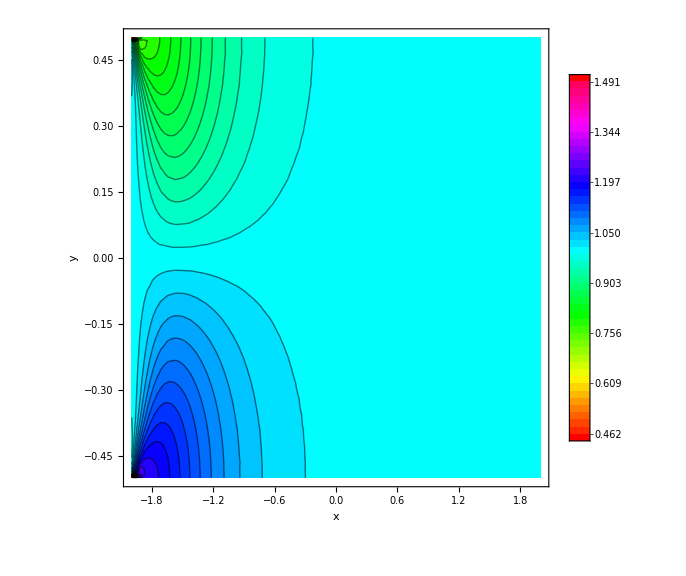

```mathematica
plotvx = ContourPlot[solution20[1]⟦IDvx-2⟧[x,y],{x,-2.0,2.0},{y,-0.5,0.5},ContourLines->True,Contours->50,PlotRange->Full,ColorFunction->Hue,ContourStyle->Black,PlotLegends->Automatic,ImageSize->Large,ContourLabels->False,FrameTicksStyle->Directive[Black,18],FrameLabel->{{Style["y",FontSize->18,FontColor->Black],None},{Style["x",FontSize->18,FontColor->Black],None}},RotateLabel->False]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Rectangle/velocity_profile_vx_e0p01.eps",plotvx]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Rectangle/velocity_profile_vx_e0p01.eps

#### vy

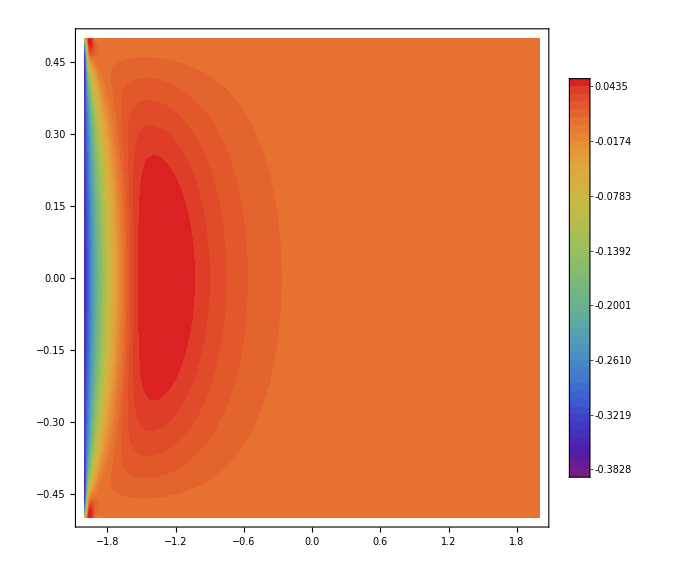

```mathematica
ContourPlot[solution20[1]⟦IDvy-2⟧[x,y],{x,-2.0,2.0},{y,-0.5,0.5},ContourLines->False,Contours->50,PlotRange->Full,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Large,ContourLabels->False]
```

### Profiles Along Different X-planes

```mathematica
xcord = -2.0;
plot=VelocityProfile[solution20,xcord];
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/vx_2p0.eps",plot]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/vx_2p0.eps

```mathematica
xcord = -1.5;
plot=VelocityProfile[solution20,xcord];
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/vx_1p5.eps",plot]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/vx_1p5.eps

```mathematica
xcord = -0.0;
plot=VelocityProfile[solution20,xcord];
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/vx_0p0.eps",plot]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/vx_0p0.eps

### Error in Velocity Profile

```mathematica
ErrorInflowVelocity = ErrorVelocityProfile[solution20,-2.0]
ErrorInflowFlux = ErrorMassFlux[solution20,-2.0]
```

{{0.001,0.012553},{0.01,0.0396502},{0.1,0.305871},{1.,1.40616},{2.,1.76051}}

{{0.001,0.00478091},{0.01,0.0356575},{0.1,0.304974},{1.,1.40616},{2.,1.76051}}

```mathematica
plot=ListLogLogPlot[{ErrorInflowVelocity,ErrorInflowFlux},PlotRange->Full,GridLines->Automatic,Frame->True,ImageSize->Large,FrameTicksStyle->Directive[Black,18],FrameLabel->{{Style["Error",FontSize->18,FontColor->Black],None},{Style["κ",FontSize->18,FontColor->Black],None}},RotateLabel->False,PlotMarkers->Automatic,Joined->True,PlotStyle->{{Thick,Darker[Green]},{Thick,Darker[Brown]}},PlotLegends->Placed[LineLegend[{Style["e^v",FontSize->18,FontColor->Black],Style["e^m",FontSize->18,FontColor->Black]}],Above]];

Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/error.eps",plot]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow/error.eps

## Solution Channel Cylinder

```mathematica
Clear[ndof]
```

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Channel_Cylinder/square_circular_cavity.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

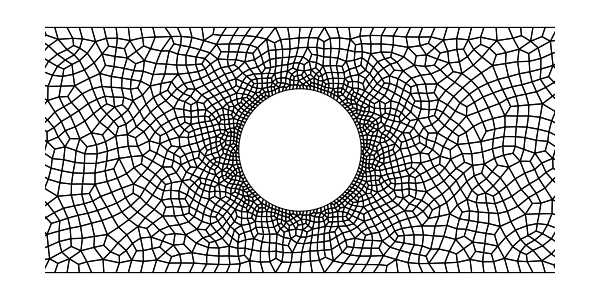

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}],PlotRange->{{-1.0,1.0},All},ImageSize->600]]
```

### G20

```mathematica
foldername = {"Tests/build/Results_2D_Channel_Cylinder/output_N6_channel_cylinder_Kn0p1"};
Do[ndof[ii] = importdata[1,1,"_global_",6,foldername⟦ii⟧]⟦8,3⟧;
numsol20[ii]=importdata[ndof[ii],1,"_global_",0,foldername⟦ii⟧];
numsol20[ii] = ConvToPrim[numsol20[ii]];
solution20[ii] = InterpolateSolution[numsol20[ii]];
entropy20[ii] = InterpolateEntropy[numsol20[ii]];
,{ii,1,Length[foldername]}];
```

Reading Data from...

../Tests/build/Results_2D_Channel_Cylinder/output_N6_channel_cylinder_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Cylinder/output_N6_channel_cylinder_Kn0p1/solution/numerical_solution_global_degree_1_DOF_146848

#### Stream Lines velocity

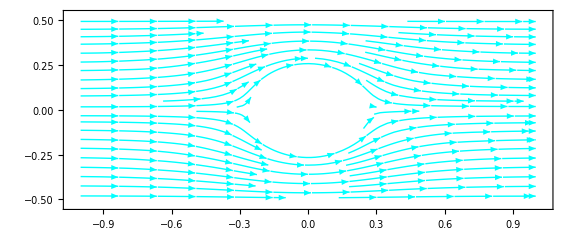

```mathematica
StreamLinesG20=PlotStreamlines[solution20[1]⟦{IDvx-2,IDvy-2}⟧,MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

#### Pressure

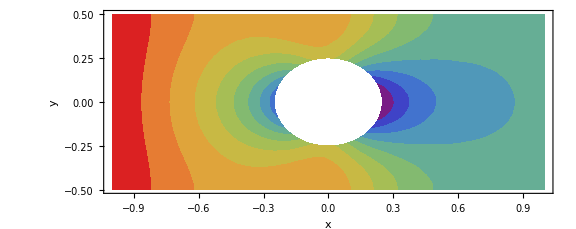

```mathematica
pressureG20=PlotContour[solution20[1]⟦IDvx-2⟧[x,y]+solution20[1]⟦IDtheta-2⟧[x,y],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

#### StremLines and Pressure

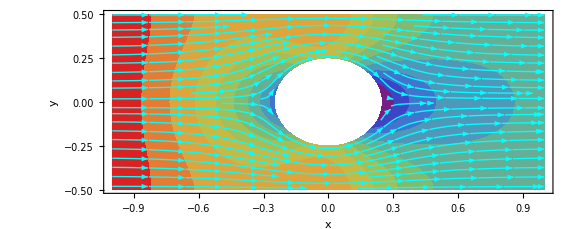

```mathematica
streamLinePressure=Show[pressureG20,StreamLinesG20]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/StreamLinePressure.eps",streamLinePressure]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/StreamLinePressure.eps

#### Temperature

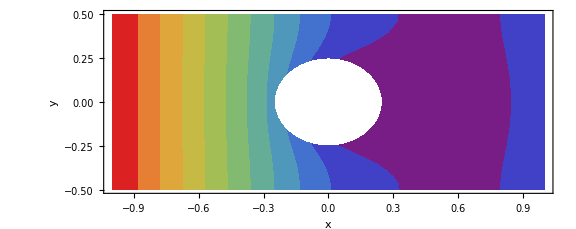

```mathematica
temperatureG20=PlotContour[solution20[1]⟦IDtheta-2⟧[x,y],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/Temperature.eps",temperatureG20]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/Temperature.eps

#### Stream Lines Heat Flux

```mathematica
StreamLinesHeatG20=PlotStreamlines[solution20[1]⟦{IDqx-2,IDqy-2}⟧,MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}];
```

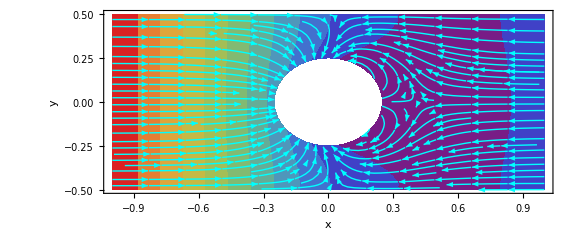

```mathematica
streamLineHeat=Show[temperatureG20,StreamLinesHeatG20]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/StreamLineHeat.eps",streamLineHeat]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/StreamLineHeat.eps

#### Temperature along the cylinder

```mathematica
tempJump = Plot[{solution20[1]⟦IDtheta-2⟧[0.28 Cos[θ],0.28Sin[θ]],1},{θ,0,π},GridLines->Automatic,Frame->True,ImageSize->Large,FrameTicksStyle->Directive[Black,18],FrameLabel->{{Style["θ̃",FontSize->18],None},{Style["ω",FontSize->18],None}},RotateLabel->False,PlotLegends->Placed[{Style["θ̃-gas",FontSize->18],Style["θ̃-wall",FontSize->18]},{0.3,0.5}]]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/tempJump.eps",tempJump]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/tempJump.eps

#### Velocity Slip along the cylinder

```mathematica
(*velocity in the tangential direction is -vx Sin θ+ vy Cos θ*)
velocitySlip = Plot[solution20[1]⟦IDvx-2⟧[0.28 Cos[θ],0.28Sin[θ]]Sin[θ]-solution20[1]⟦IDvy-2⟧[0.28Cos[θ],0.28Sin[θ]]Cos[θ],{θ,0,π},GridLines->Automatic,Frame->True,ImageSize->Large,FrameTicksStyle->Directive[Black,18],FrameLabel->{{Style["(ṽ)_t",FontSize->18,FontColor->Black],None},{Style["ω",FontSize->18,FontColor->Black],None}},RotateLabel->False]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/velocitySlip.eps",velocitySlip]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/velocitySlip.eps

### G56

```mathematica
foldername = {"Tests/build/Results_2D_Channel_Cylinder/output_N12_channel_cylinder_Kn0p1"};
Do[ndof[ii] = importdata[1,1,"_global_",6,foldername⟦ii⟧]⟦8,3⟧;
numsol56[ii]=importdata[ndof[ii],1,"_global_",0,foldername⟦ii⟧];
numsol56[ii] = ConvToPrim[numsol56[ii]];
solution56[ii] = InterpolateSolution[numsol56[ii]];
entropy56[ii] = InterpolateEntropy[numsol56[ii]];
,{ii,1,Length[foldername]}];
```

Reading Data from...

../Tests/build/Results_2D_Channel_Cylinder/output_N12_channel_cylinder_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Cylinder/output_N12_channel_cylinder_Kn0p1/solution/numerical_solution_global_degree_1_DOF_384064

### G120

```mathematica
foldername = {"Tests/build/Results_2D_Channel_Cylinder/output_N20_channel_cylinder_Kn0p1"};
Do[ndof[ii] = importdata[1,1,"_global_",6,foldername⟦ii⟧]⟦8,3⟧;
numsol120[ii]=importdata[ndof[ii],1,"_global_",0,foldername⟦ii⟧];
numsol120[ii] = ConvToPrim[numsol120[ii]];
solution120[ii] = InterpolateSolution[numsol120[ii]];
entropy120[ii] = InterpolateEntropy[numsol120[ii]];
,{ii,1,Length[foldername]}];
```

Reading Data from...

../Tests/build/Results_2D_Channel_Cylinder/output_N20_channel_cylinder_Kn0p1/computational_parameters.txt

Reading Data from...

../Tests/build/Results_2D_Channel_Cylinder/output_N20_channel_cylinder_Kn0p1/solution/numerical_solution_global_degree_1_DOF_790720

#### Stream Lines

```mathematica
StreamLinesG20=PlotStreamlines[solution20[1]⟦{IDvx-2,IDvy-2}⟧,MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

#### Pressure

```mathematica
pressureG20=PlotContour[solution20[1]⟦IDvx-2⟧[x,y]+solution20[1]⟦IDtheta-2⟧[x,y],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

#### StremLines and Pressure

```mathematica
streamLinePressure=Show[pressureG20,StreamLinesG20]
```

-Graphics-

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/StreamLinePressure.eps",streamLinePressure]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/StreamLinePressure.eps

#### Temperature

```mathematica
temperatureG20=PlotContour[solution20[1]⟦IDtheta-2⟧[x,y],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/Temperature.eps",temperatureG20]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/Temperature.eps

### Error in Entropy

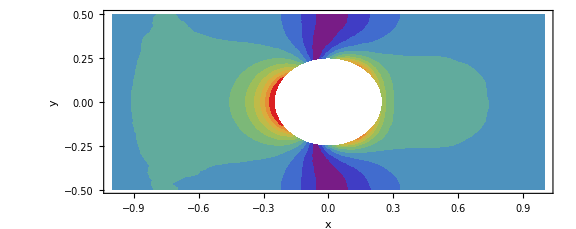

```mathematica
errorEntropyG20G56=PlotContour[Abs[entropy20[1][x,y]-entropy120[1][x,y]],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/errroEntropyG20G120.eps",errorEntropyG20G56]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/errroEntropyG20G120.eps

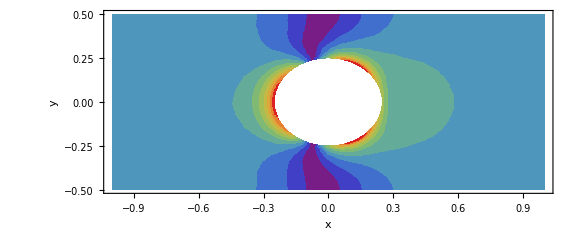

```mathematica
errorEntropyG56G120=PlotContour[Abs[entropy56[1][x,y]-entropy120[1][x,y]],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

```mathematica
Export["/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/errroEntropyG56G120.eps",errorEntropyG56G120]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/entropy_stable_inflow_outflow/results/2D_flow_Cylinder/errroEntropyG56G120.eps